## Gravito-scalar QNMs of Schwarzschild BHs in Dynamical Chern-Simons gravity Reference: Paolo Pani, “Advanced methods in Black-Hole Perturbation Theory” (2013)

#### Perturbation equations:

```mathematica
Clear[u1,u2];
ϵa=1;
F[r_]:=1-2M/r;
V1=F[r]((l(l+1))/r^2-(6M)/r^3);
V2=F[r]((l(l+1))/r^2(1+(576 π M^2 α^2)/(β r^6))+(2M)/r^3);
S1=F[r]((96 I π M ω α)/r^5);
S2=F[r](Factorial[l+2]/Factorial[l-2](6 M I α)/(β r^5 ω));
e1=F[r]^2 u1''[r]+F'[r]F[r]u1'[r]+(ω^2-V1)u1[r]-S1 u2[r]  (* 39 a *)(* expressed in radial coords. If in tortoise coords F[r]^2 u1''[r]+F'[r]F[r]u1'[r] = u1''[r*] *)
e2=F[r]^2 u2''[r]+F'[r]F[r]u2'[r]+(ω^2-V2)u2[r]-S2 u1[r] (* 39 b *)
```

(-(-(6 M)/r^3+(l (1+l))/r^2) (1-(2 M)/r)+ω^2) u1[r]-(96 ⅈ M π (1-(2 M)/r) α ω u2[r])/r^5+(2 M (1-(2 M)/r) u1'[r])/r^2+(1-(2 M)/r)^2 u1''[r]

-(6 ⅈ M (1-(2 M)/r) α (2+l)! u1[r])/(r^5 β ω (-2+l)!)+(-(1-(2 M)/r) ((2 M)/r^3+(l (1+l) (1+(576 M^2 π α^2)/(r^6 β)))/r^2)+ω^2) u2[r]+(2 M (1-(2 M)/r) u2'[r])/r^2+(1-(2 M)/r)^2 u2''[r]

#### Series at the horizon [arbitrary order]

```mathematica
Clear[u1,u2];

u1[r_]:=(r-2M)^bb G1[r]; (* Frobenius solution eq. 30 back in radial coordinates*)
u2[r_]:=(r-2M)^bb G2[r];
Es1=FullSimplify[(r^6 e1)/(-2 M+r)^bb]
Es2=FullSimplify[e2/(1/(r^9 β ω Gamma[-1+l])(-2 M+r)^bb)];
```

r^2 (-12 M^2+2 (3+bb+l+l^2) M r+r^2 ((-1+bb) bb-l (1+l)+r^2 ω^2)) G1[r]+(2 M-r) (96 ⅈ M π α ω G2[r]-r^3 (2 (M+bb r) G1'[r]+r (-2 M+r) G1''[r]))

```mathematica
ORD=5;
G1[r_]:=Sum[u1h[i](r-2M)^i,{i,0,ORD+3}];
G2[r_]:=Sum[u2h[i](r-2M)^i,{i,0,ORD+3}];
ss=Series[{Es1,Es2}/.{bb->-2 ⅈ M ω},{r,2M,ORD+3}];
FullSimplify[Series[Es1/.{bb->-2 ⅈ M ω},{r,2M,1}]] (* series expansion of the equation of motion in r around 2M as the Frobenius expansion is around r - r+ = r - 2M *)
yh=Union[Table[u1h[i],{i,1,ORD}],Table[u2h[i],{i,1,ORD}]];
EQsh=Union[Table[Normal[Series[SeriesCoefficient[ss[[1]],i],{J,0,1}]]==0,{i,1,ORD}],Table[Normal[Series[SeriesCoefficient[ss[[2]],i],{J,0,1}]]==0,{i,1,ORD}]];
Length[yh]
Length[EQsh]
seriesH=Solve[EQsh,yh][[1]]

Clear[u1,u2,G1,G2]
```

-8 ((-3+l+l^2) M^3 u1h[0]+M^4 (-2 ⅈ ω u1h[0]-2 u1h[1])-8 M^5 ω (ω u1h[0]-ⅈ u1h[1])+12 ⅈ M π α ω u2h[0]) (r-2 M)+O[r-2 M]^2

10

10

{u1h[1]→-(4 M^2 (6+16 M^3 ω^2) u1h[0]-96 ⅈ M π α ω u2h[0])/(16 M^4-64 ⅈ M^5 ω),8,u2h[5]→-(566+1)/(122880 7 (1))}
 |  |  |  |

```mathematica
Solve[bb^2 M^2+4 M^4 ω^2==0,bb] (* why does bb comes from this? *)
```

{{bb→-2 ⅈ M ω},{bb→2 ⅈ M ω}}

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["seriesH.mx",{seriesH,ORD}];
```

#### Series at infinity [arbitrary order]

```mathematica
u1[r_]:=Exp[kk r] r^n G1[r];
u2[r_]:=Exp[kk r] r^n G2[r]; (* the frobeniussolution, eq (30) evaluated at r >> r+, see also eq. (11) *)
Es1=FullSimplify[e1/(ⅇ^(kk r) r^n)]
Es2=FullSimplify[e2/(ⅇ^(kk r) r^n)];
```

1/r^6(r^2 ((-2 M+r) (r (-(1+l-n) (l+n)+2 kk n r+kk^2 r^2)-2 M (-3+n^2+2 n (-1+kk r)+kk r (-1+kk r)))+r^4 ω^2) G1[r]+(2 M-r) (96 ⅈ M π α ω G2[r]-r^3 (2 (M (1-2 n-2 kk r)+r (n+kk r)) G1'[r]+r (-2 M+r) G1''[r])))

```mathematica
ORDinf=2;
G1[r_]:=Sum[u1inf[i]/r^i,{i,0,ORDinf+3}];
G2[r_]:=Sum[u2inf[i]/r^i,{i,0,ORDinf+3}];
ruleINF={kk^2->-ω^2,n->-(2 M ω^2)/kk};
ss=Series[{Es1,Es2},{r,∞,ORDinf+3}]/.ruleINF; 
(* expands in 1/r up to 1/r^5, such that each order indclues one more unkown from the expansion to be solved iteritivly, note that 1/r^5 is the first order where the equations u1 and u2 mix *)
yinf=Union[Table[u1inf[i],{i,1,ORDinf+1}],Table[u2inf[i],{i,1,ORDinf+1}]];
(* the list of variables to be solved for *)
EQsinf=Union[Table[SeriesCoefficient[ss[[1]],i]==0,{i,2,ORDinf+2}],Table[SeriesCoefficient[ss[[2]],i]==0,{i,2,ORDinf+2}]];
(* puts each coefficent into its own equation via linear independance *)
Length[yinf]
Length[EQsinf]
seriesINF=Solve[EQsinf,yinf][[1]]//Simplify
(* soves the linear equations for the cooeficents in the expansion G in terms of the boundary values uinf *)
Clear[u1,u2,G1,G2]
```

6

6

{u1inf[1]→1/(2 kk^3)(2 kk^3 M+2 kk M ω^2+4 M^2 ω^4-kk^2 (l+l^2-12 M^2 ω^2)) u1inf[0],u1inf[2]→1/(8 kk^6)(12 kk^6 M^2+32 kk M^3 ω^6+16 M^4 ω^8+8 kk^5 M (2-l-l^2+14 M^2 ω^2)+4 kk^2 M^2 ω^4 (5-2 l-2 l^2+24 M^2 ω^2)+4 kk^3 M ω^2 (1-2 l-2 l^2+28 M^2 ω^2)+kk^4 (2 l^3+l^4+16 M^2 ω^2 (2+9 M^2 ω^2)-2 l (1+12 M^2 ω^2)-l^2 (1+24 M^2 ω^2))) u1inf[0],u1inf[3]→1/(48 kk^9)(120 kk^9 M^3+288 kk M^5 ω^10+64 M^6 ω^12+16 kk^2 M^4 ω^8 (31-3 l-3 l^2+36 M^2 ω^2)+24 kk^3 M^3 ω^6 (17-6 l-6 l^2+76 M^2 ω^2)+4 kk^8 M^2 (58-23 l-23 l^2+364 M^2 ω^2)+4 kk^4 M^2 ω^4 (40+6 l^3+3 l^4+516 M^2 ω^2+432 M^4 ω^4-36 l^2 (1+2 M^2 ω^2)-3 l (13+24 M^2 ω^2))+6 kk^5 M ω^2 (4+6 l^3+3 l^4+196 M^2 ω^2+656 M^4 ω^4-4 l (3+22 M^2 ω^2)-l^2 (9+88 M^2 ω^2))+6 kk^7 M (6 l^3+3 l^4-2 l (7+40 M^2 ω^2)-l^2 (11+80 M^2 ω^2)+4 (4+49 M^2 ω^2+132 M^4 ω^4))-kk^6 (3 l^5+l^6-3 l^3 (5+24 M^2 ω^2)-l^4 (5+36 M^2 ω^2)+4 l^2 (1+65 M^2 ω^2+108 M^4 ω^4)+4 l (3+74 M^2 ω^2+108 M^4 ω^4)-8 M^2 ω^2 (49+346 M^2 ω^2+216 M^4 ω^4))) u1inf[0],u2inf[1]→1/(2 kk^3)(2 kk^3 M+2 kk M ω^2+4 M^2 ω^4-kk^2 (l+l^2-12 M^2 ω^2)) u2inf[0],u2inf[2]→1/(8 kk^6)(12 kk^6 M^2+32 kk M^3 ω^6+16 M^4 ω^8-8 kk^5 M (l+l^2-14 M^2 ω^2)+4 kk^2 M^2 ω^4 (5-2 l-2 l^2+24 M^2 ω^2)+4 kk^3 M ω^2 (1-2 l-2 l^2+28 M^2 ω^2)+kk^4 (2 l^3+l^4+16 M^2 ω^2 (2+9 M^2 ω^2)-2 l (1+12 M^2 ω^2)-l^2 (1+24 M^2 ω^2))) u2inf[0],u2inf[3]→1/(48 kk^6)(32 kk^3 M^2 (kk+2 M ω^2)^2-4 M (18 kk^3 M+10 kk M ω^2+4 M^2 ω^4-kk^2 (-6+l+l^2-12 M^2 ω^2)) (2 kk^3 M+6 kk M ω^2+8 M^2 ω^4-kk^2 (-1+l+l^2-8 M^2 ω^2))+1/kk^3(2 kk^3 M+2 kk M ω^2+4 M^2 ω^4-kk^2 (l+l^2-12 M^2 ω^2)) (132 kk^6 M^2+64 kk M^3 ω^6+16 M^4 ω^8+4 kk^2 M^2 ω^4 (23-2 l-2 l^2+24 M^2 ω^2)+8 kk^3 M ω^2 (7-2 l-2 l^2+30 M^2 ω^2)+4 kk^5 M (12-5 l-5 l^2+68 M^2 ω^2)+kk^4 (2 l^3+l^4-8 l (1+3 M^2 ω^2)-l^2 (7+24 M^2 ω^2)+12 (1+16 M^2 ω^2+12 M^4 ω^4)))) u2inf[0]}

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["seriesINF.mx",{seriesINF,ORDinf}];
```

#### Higher order BCs at infinity

```mathematica
(*<<"seriesINF.mx";*)

(* matching the the frobenius solution, eq (30) evaluated at r >> r+ with eq. (28)  *)
(* seriesINF is a list of rules of what u1inf[i≠0] is in terms of u1inf[0] and simmilarly for u2inf (hence union) *)
(* orderinf = 2 *)

(* These are simplified versions of the real code so that you can see what happens *)
ORDinf2=(ORDinf+1);
testSINF = { u1inf[1]-> a1 u1inf[0] + b1 u1inf[0],u1inf[2]-> a2 u1inf[0] + b2 u1inf[0],u1inf[3]-> a3 u1inf[0] + b3 u1inf[0]};
"The sum at inf"
test1 = (Sum[u1inf[i]/r^i,{i,0,ORDinf2}]//.Union[testSINF,{u1inf[0]->B1,u2inf[0]->B2,kk->-k}]) Exp[-k r] r^((2 M ω^2)/k)
"The derivative of the sum at inf"
dtest1 = D[test1,r]



(* real code from here *)
y1=(Sum[u1inf[i]/r^i,{i,0,ORDinf2}]//.Union[seriesINF,{u1inf[0]->B1,u2inf[0]->B2,kk->-k}]) Exp[-k r] r^((2 M ω^2)/k)+ (Sum[u1inf[i]/r^i,{i,0,ORDinf2}]//.Union[seriesINF,{u1inf[0]->C1,u2inf[0]->C2,kk->k}]) Exp[k r] r^(-(2 M ω^2)/k);
y1p=D[y1,r];
y2= (Sum[u2inf[i]/r^i,{i,0,ORDinf2}]//.Union[seriesINF,{u1inf[0]->B1,u2inf[0]->B2,kk->-k}]) Exp[-k r] r^((2 M ω^2)/k)+(Sum[u2inf[i]/r^i,{i,0,ORDinf2}]//.Union[seriesINF,{u1inf[0]->C1,u2inf[0]->C2,kk->k}]) Exp[k r] r^(-(2 M ω^2)/k);
y2p=D[y2,r];
solBC=Solve[{y1==Y1,y1p==Y1p,y2==Y2,y2p==Y2p},{B1,C1,B2,C2}];
(* A list of rules for how to replace B1, B2, C1, C2 in favour of Y1 and Y1p *)
solBC=solBC[[1]];
```

The sum at inf

ⅇ^(-k r) (B1+(a3 B1+B1 b3)/r^3+(a2 B1+B1 b2)/r^2+(a1 B1+b1 B1)/r) r^((2 M ω^2)/k)

The derivative of the sum at inf

ⅇ^(-k r) (-(3 (a3 B1+B1 b3))/r^4-(2 (a2 B1+B1 b2))/r^3-(a1 B1+b1 B1)/r^2) r^((2 M ω^2)/k)-ⅇ^(-k r) k (B1+(a3 B1+B1 b3)/r^3+(a2 B1+B1 b2)/r^2+(a1 B1+b1 B1)/r) r^((2 M ω^2)/k)+1/k 2 ⅇ^(-k r) M (B1+(a3 B1+B1 b3)/r^3+(a2 B1+B1 b2)/r^2+(a1 B1+b1 B1)/r) r^(-1+(2 M ω^2)/k) ω^2

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["solBC.mx",{solBC}];
```

```mathematica
Length[solBC]
```

4

### Integrator:

```mathematica
SetDirectory[NotebookDirectory[]];
(* 
ω0 - qnm frequency
α0 - dcs coupling parameter
u10 - the boundary condition at the horison for the first field equation
u20 - the boundary condition at the horison for the second field equation
l0 - spin of field 
eps - step from the horison
inf - step at infinity

params not arguments 
M - mass of BH
β - ?

 *)
(* note that we give a value for ω and it is not found. The integrator does not make use of the boundary at inf. *)
INT[ω0_,α0_,u10_,u20_,l0_,EPS_,INF_]:=(
ruleP={AccuracyGoal->80,PrecisionGoal->12,MaxSteps->10^5};
ruleP={};

param={M->1,l->l0,ω->ω0,u1h[0]->u10,u2h[0]->u20,β->1,α->α0};
rhn=2M(1+EPS)/.param;
rinf=INF;

(* ord = order we calculate to *)

(*<<"seriesH.mx";*)
(* recall seriesH is the solution found from the horizon *)
(* -8 ((-3+l+l^2) M^3 u1h[0]+M^4 (-2 ⅈ ω u1h[0]-2 u1h[1])-8 M^5 ω (ω u1h[0]-ⅈ u1h[1])+12 ⅈ M π α ω u2h[0]) (r-2 M)+O[r-2 M]^2 *)

u1g=(r-2M)^(-2I ω M)Sum[u1h[i](r-2M)^i,{i,0,ORD}]//.Union[param,seriesH]; 
u2g=(r-2M)^(-2I ω M)Sum[u2h[i](r-2M)^i,{i,0,ORD}]//.Union[param,seriesH]; (* eq.30 *)

(* im not sure why this is typed out explicitly when we had to find it in the first section? So it doesnt need the first section to run as we import seriesH.mx ? *)
EQs={(-(-(6 M)/r^3+(l (1+l))/r^2) (1-(2 M)/r)+ω^2) u1[r]-(96 ⅈ M π (1-(2 M)/r) α ω u2[r])/r^5+(2 M (1-(2 M)/r) u1'[r])/r^2+(1-(2 M)/r)^2 u1''[r]==0,-(6 ⅈ M (1-(2 M)/r) α (2+l)! u1[r])/(r^5 β ω (-2+l)!)+(-(1-(2 M)/r) ((2 M)/r^3+(l (1+l) (1+(576 M^2 π α^2)/(r^6 β)))/r^2)+ω^2) u2[r]+(2 M (1-(2 M)/r) u2'[r])/r^2+(1-(2 M)/r)^2 u2''[r]==0}//.param;
BCs={u1[rhn]==u1g/.r->rhn,u1'[rhn]==D[u1g,r]/.r->rhn,u2[rhn]==u2g/.r->rhn,u2'[rhn]==D[u2g,r]/.r->rhn};
sol=NDSolve[Union[EQs,BCs],{u1,u2},{r,rhn,rinf},ruleP];
u1n=u1[r]/.sol[[1]];
u2n=u2[r]/.sol[[1]]; 
(* solution at the horison *)

);
```

```mathematica
INT[0.1-0.1I,1,1,1,2,10^-4,10^2];
{u1n,u2n}/.r->rinf
(* the numerical solution for the field in terms of the Frobenius solution (30) for the given value of ω is found by INT. Used in constructing the matrix S(ω)*)
```

{6.25717×10^10-1.14749×10^11 ⅈ,-3.35374×10^11-1.07638×10^12 ⅈ}

#### DETERMINANT

```mathematica
SetDirectory[NotebookDirectory[]];
(* 
ω0 - qnm frequency
α0 - dcs coupling parameter
l0 - spin of field 
eps - step from the horison
inf - step at infinity
 *)
(* This finds the matric S(ω) which when evaluated at the horizon and set to zero is a function for ω *)
LINCOMB[ω0_,α0_,l0_,EPS_,INF_]:=(

<<"polar_solBC.mx";

(* we have a 2d field space and so we need to consider boundary conditions at the horison for the basis (1,0) and (0,1) (or any other basis) in order to make the matrix S, see (23), where the row corispons to one field varying the basis, and collomn holding the basis const and varing the field. Hence we need to call INT for both basis eleements, each time giving a colomn *)

INT[ω0,α0,1,0,l0,EPS,INF]; 
Print["solutions at rinf 1,0"];
Print[{u1n,u2n}/.r->rinf];
(* u1n - the numerical solutions made within INT *)
u110=u1n;
u210=u2n;
u110p=D[u1n,r];
u210p=D[u2n,r];
(* recall solBC are the boundary conditions at inf *)
rule10=Union[solBC,param,{k->I ω,Y1->u110,Y1p->u110p,Y2->u210,Y2p->u210p,r->rinf}];
(* B and C are the coefs in Higher order BCs at infinity as in eq.(8) *)
B110=B1//.rule10;
C110=C1//.rule10;
B210=B2//.rule10;
C210=C2//.rule10;

INT[ω0,α0,0,1,l0,EPS,INF];
Print["solutions at rinf 0,1"];
Print[{u1n,u2n}/.r->rinf];
u101=u1n;
u201=u2n;
u101p=D[u1n,r];
u201p=D[u2n,r];
rule01=Union[solBC,param,{k->I ω,Y1->u101,Y1p->u101p,Y2->u201,Y2p->u201p,r->rinf}];
B101=B1//.rule01;
C101=C1//.rule01;
B201=B2//.rule01;
C201=C2//.rule01;
(************)
BB=B110 B201-B101 B210;
CC=C110 C201-C101 C210;
{BB, CC}(*BB for QNMs, CC for quasi-bound states*)
)
```

```mathematica
LINCOMB[0.1+0.0001I,1,2,10^-6,10^2]
```

{0.1+0.0001 ⅈ,1,1,0,2,1/1000000,100}

NDSolve::ndsz: At r == 87.841, step size is effectively zero; singularity or stiff system suspected.

solutions at rinf 1,0

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

{5.99299×10^57+1.45341×10^57 ⅈ,0.+0. ⅈ}

InterpolatingFunction::dmval: Input value {100} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.1+0.0001 ⅈ,1,0,1,2,1/1000000,100}

NDSolve::ndsz: At r == 2., step size is effectively zero; singularity or stiff system suspected.

solutions at rinf 0,1

{-4.22236×10^14+2.40209×10^14 ⅈ,-7.65014×10^13-2.31871×10^14 ⅈ}

{-1.47775×10^72-5.06267×10^71 ⅈ,1.43399×10^72-7.71445×10^71 ⅈ}

#### Find root:

```mathematica
ωguess=0.48-0.1 ⅈ;(*grav*)
ωguess=0.3-0.1 ⅈ;(*scal*)
(**************************************************)

f4[y_?NumericQ]:=LINCOMB[y,10^-3,2,1 10^-3,30][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}(*,AccuracyGoal->2,PrecisionGoal->12*)][[1]]
(* The roots of LINCOMB are the qnm *)
Abs[f4[y0n]]
```

0.373042-0.0886204 ⅈ

4.02918×10^-10

### Tracking

```mathematica
xi=10^-3;
xf=0.8;
dim=60;
dx=(xf-xi)/dim;
TT=Table[Null,{dim}];
xx=xi;
(****)
α00=xi;

ωguess=2.0551788732666325-0.09533427763819255 ⅈ;(*l=10*)
ωguess=1.40974-0.0955096 I;(*l=7*)
ωguess=0.48-0.1 ⅈ;(*grav*)
ωguess=0.3-0.1 ⅈ;(*scal*)



(****)
Monitor[For[j=1,j<dim+1,{
(* xx - DCS coupling parameter, y - ω, 10 - angular number, numerial approx to r+ and inf *)
f4[y_?NumericQ]:=LINCOMB[y,xx,10,10^-3,3 10^1][[1]];
(* find root returns a list of rules, in this case y-> f4^-1(0) *)
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}(*,AccuracyGoal->12,PrecisionGoal->12*)][[1]];
check=Abs[f4[y0n]];
TT[[j]]={N[xx],y0n,check};(* N - gives the numerical value of xx *)
(* TT stores the value of the DCS paramiter, the value of ω found for this itteration and how close to the root its is *)
ωguess=y0n;
(* after finding a root, a small change of the DCS paramiter will not move the value of ω will not change much and so the next guess should be the previusly found value *)
xx=xx+dx; (* slightly faster than xi + j*dx *)
j++;
}],{j,N[xx],y0n,check}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["TT.mx",{TT}];
```

```mathematica
TR=Table[{TT[[i]][[1]],Re[TT[[i]][[2]]]},{i,1,Length[TT]}];
TI=Table[{TT[[i]][[1]],Im[TT[[i]][[2]]]},{i,1,Length[TT]}];
```

```mathematica
TR1=TR;
TI1=TI;
```

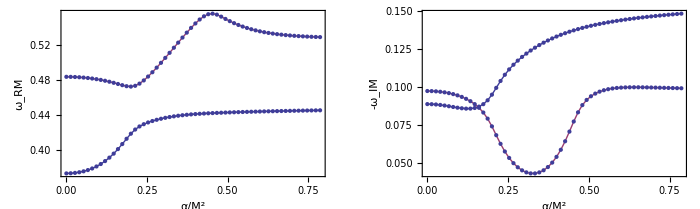

```mathematica
(***)
p1=ListPlot[{TR1,TR2},Frame->True,Joined->True,Mesh->All,FrameLabel->{"α/M^2","ω_RM"},Axes->False];
p2=ListPlot[{Abs[TI1],Abs[TI2]},Frame->True,Joined->True,Mesh->All,FrameLabel->{"α/M^2","-ω_IM"},PlotRange->All,Axes->False];
GraphicsGrid[{{p1,p2}},ImageSize->700]
```

### Higher-l

```mathematica
ωguess=0.48-0.1 ⅈ;(*grav*)
ωguess=0.3-0.1 ⅈ;(*scal*)
ωguess=1.40974-0.0955096 I;(*l=7*)
ωguess=1.9916474515518394-0.287911944390142 I;(*l=10*)
ωguess=2-0.3 I;(*l=10*)
(*ωguess=0.7337751980725775-0.127070807565408 ⅈ;(*scal*)*)
(**************************************************)

f4[y_?NumericQ]:=LINCOMB[y,0,10,1 10^-3,40][[1]];
y0n=y/.FindRoot[f4[y]==0,{y,ωguess}(*,AccuracyGoal->2,PrecisionGoal->12*)][[1]]
Abs[f4[y0n]]
```

2.04925-0.10088 ⅈ

5.40477×10^-10